## LIBR

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
```

## APPLICATIONS

## tmp-movie_protocol_IN-DEV

```mathematica
(*
Table[gLine[{k,If[k<=10,k,11-Mod[k,10]]},Color->Cyan,Thickness->0.0025],{k,2,19}]//toGL//gr
 f[x_,y_]:=Table[gLine[{x,y},pGon[128][[k]],Color->Gray,Thickness->0.0025],{k,1,128}]//toGL//gr
f[-0.5,-0.5]
gAnimation=ConstantArray[0,101]
Table[{k,k},{k,-0.5,0.5,0.01}]//Length
For[k=1,k<=101,k++,gAnimation[[k]]=f[-0.51+ k/100,-0.51+ k/100]]
Export["movie.avi",gAnimation]
*)
```

## DEV

## Three Reflections Theorem

### Introduction

-Graphics-

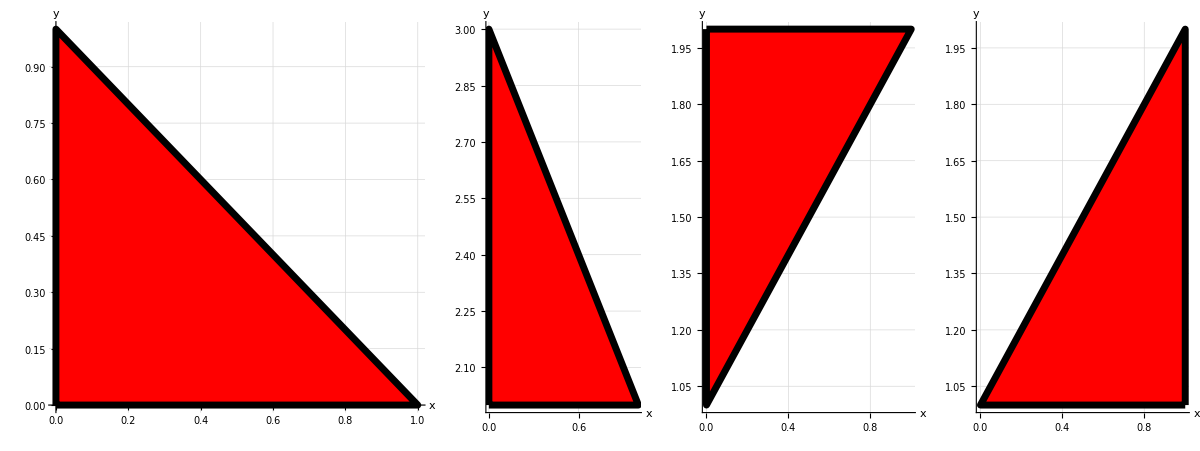

```mathematica
GraphicsRow[
{
gPolygon[{{0,0},{1,0},{0,1}}]//toGL//gr1,
tra3[gPolygon[{{0,0},{1,0},{0,1}}],{0,2}]//toGL//gr1,
rot3[tra3[gPolygon[{{0,0},{1,0},{0,1}}],{0,2}],{3/2Pi/1,{0,2}}]//toGL//gr1,
ref3[rot3[tra3[gPolygon[{{0,0},{1,0},{0,1}}],{0,2}],{3/2Pi/1,{0,2}}],{{-1,1},{0,1}}]//toGL//gr1
}
]
```

### Translation :> Reflections

```mathematica
traM:={{1,0,0},{0,1,2},{0,0,1}}
ptsM:={{0,1,0},{0 ,0,1},{1,1,1}}

traM//mf
ptsM//mf
```

(1 | 0 | 0
0 | 1 | 2
0 | 0 | 1)

(0 | 1 | 0
0 | 0 | 1
1 | 1 | 1)

```mathematica
traM.ptsM//mf
```

(0 | 1 | 0
2 | 2 | 3
1 | 1 | 1)

### tmp

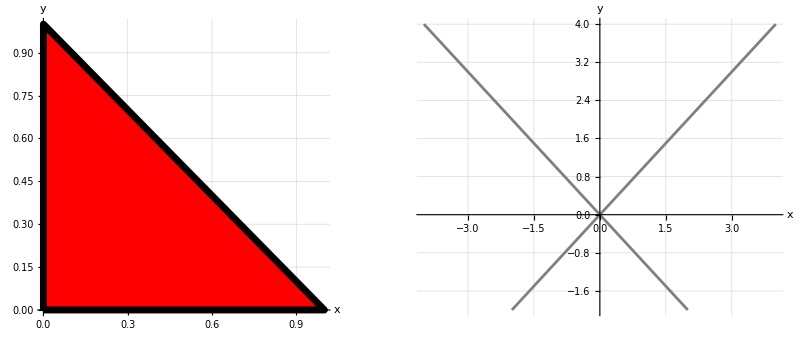

{1,1}

{-1,1}

```mathematica
figdemo:=gPolygon[{{0,0},{1,0},{0,1}}];
GraphicsRow[
{
figdemo//toGL//gr1,
{
gLine[{-2,-2},{4,4},Color->Gray, Thickness->0.005]//toGL,
gLine[{2,-2},{-4,4},Color->Gray, Thickness->0.005]//toGL}//gr1
}
]
({4,4}-{-2,-2})/6
({-4,4}-{2,-2})/6
```

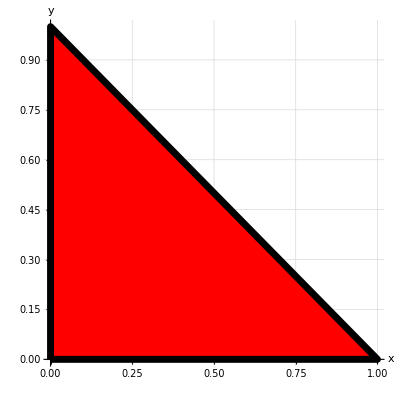

```mathematica
figdemo//toGL//gr1
```

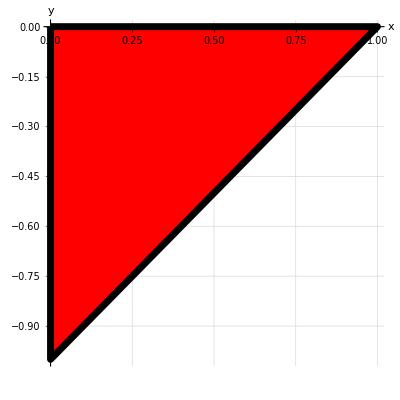

```mathematica
ref3[figdemo,{{0,1},{0,0}}]//toGL//gr1
```

```mathematica
mat1:={{0,-3},{3,0}}
mat2:={{0,-3,-3},{3,0,3},{3,-3,0}}
```

```mathematica
mat2//mf
-Transpose[mat2]//mf
```

(0 | -3 | -3
3 | 0 | 3
3 | -3 | 0)

(0 | -3 | -3
3 | 0 | 3
3 | -3 | 0)

```mathematica
MatrixExp[mat1]
MatrixExp[mat2]//N//Det
```

{{Cos[3],-Sin[3]},{Sin[3],Cos[3]}}

1.

```mathematica
Transpose[MatrixExp[mat1]]//mf
MatrixExp[Transpose[mat1]]//mf
```

(Cos[3] | Sin[3]
-Sin[3] | Cos[3])

(Cos[3] | Sin[3]
-Sin[3] | Cos[3])

## Quaternions

```mathematica
m1:=IdentityMatrix[2]
mI:={{0,-1},{1,0}}
mJ:={{0,-I},{-I,0}}
mK:={{I,0},{0,-I}}
```

```mathematica
((8 mI) .(2mK)+(4mI).(2mJ)).Inverse[mI+mK]//mf
```

(4-8 ⅈ | -8+4 ⅈ
8+4 ⅈ | 4+8 ⅈ)

```mathematica
(x1 m1+x2 mI+x3 mJ+x4 mK)//mf
Det[(x1 m1+x2 mI+x3 mJ+x4 mK)]
```

(x1+ⅈ x4 | -x2-ⅈ x3
x2-ⅈ x3 | x1-ⅈ x4)

x1^2+x2^2+x3^2+x4^2

```mathematica
(4 m1+8 mI-4 mJ-8 mK)//mf
Det[(4 m1+8 mI-4 mJ-8 mK)]
```

(4-8 ⅈ | -8+4 ⅈ
8+4 ⅈ | 4+8 ⅈ)

160

```mathematica
matToQuaternion[mat_]:={Re[mat[[1,1]]],Re[mat[[2,1]]],-Im[mat[[1,2]]],Im[mat[[1,1]]]}
matToQuaternion[((x1 m1) +(1mI)+(1mJ)+(1mK)).Inverse[m1]]
```

{Re[x1],1,1,1+Im[x1]}

```mathematica
mI.mK//mf
```

(0 | ⅈ
ⅈ | 0)